```mathematica
(*s=InputString["Enter xml file name","tooth.xml"]//StringReplace[#," "->""]&;*)
(*xml=Import[NotebookDirectory[]<>"~images\\"<>"nucleon_naive.xml"];*)
(*xml=Import[NotebookDirectory[]<>"~images\\"<>"nucleon_strong_red.xml"];*)
(*xml=Import[NotebookDirectory[]<>"~images\\"<>"nucleon_weak_red.xml"];*)
(*xml=Import[NotebookDirectory[]<>"~images\\"<>"nucleon_naive_optimized_green_1000.xml"];*)
(*xml=Import[NotebookDirectory[]<>"~images\\"<>"nucleon_naive_optimized_red_1000.xml"];*)
xml=Import[NotebookDirectory[]<>"~images\\"<>"CT-Knee_naive.xml"];
{tfifile,volumefile,legends,face,imagefilenames,txtfilenames,{featurefilename,visibilityfilename},resultxml,imagefile,rawfile,dataname}=xml;
(*Column[xml,Background->{{Lighter@LightYellow,Lighter@LightBlue}},Frame->True,FrameStyle->Directive[LightGray,Thin,Dashed]]*)

tf=Import[tfifile,"XML"];
bincount=256;
intensity=ToExpression@Cases[tf,XMLElement["intensity",{"value"->atrib_,___},___]:>atrib,∞];
r=ToExpression@Cases[tf,XMLElement["colorL",{"r"->atrib_,___},___]:>atrib,∞];
g=ToExpression@Cases[tf,XMLElement["colorL",{___,"g"->atrib_,___},___]:>atrib,∞];
b=ToExpression@Cases[tf,XMLElement["colorL",{___,"b"->atrib_,___},___]:>atrib,∞];
a=ToExpression@Cases[tf,XMLElement["colorL",{___,"a"->atrib_},___]:>atrib,∞];
rgbcolors=(#/255.&)/@Transpose[{r,g,b}]//(RGBColor/@#&);
rgbfunction=(Blend[Transpose[{intensity,rgbcolors}], #1] & );
rgba=(#/255.&)/@Transpose[{r,g,b,a}]//(RGBColor/@#&);
rgbafunction=(Blend[Transpose[{intensity,rgba}], #1] & );
alpha=(#/255.&)/@a;

d = Import[volumefile,"Image3D"];
colorized=Image3D[d,ColorFunction->rgbafunction];
{lightness,chroma,hue,opacity}=ImageApply[List@@rgbafunction[#]&,d]//Image3D[#,ColorSpace->"RGB"]&//ColorSeparate[ColorConvert[#,"LCH"]]&;
(*lo=ImageMultiply[lightness,opacity];
co=ImageMultiply[chroma,opacity];*)
(*g1=ImageDifference[GaussianFilter[lightness,{2,Sqrt[2]/8.*2}],GaussianFilter[lightness,{4,Sqrt[2]/8.*4}]]
g2=ImageDifference[GaussianFilter[chroma,{2,Sqrt[2]/8.*2}],GaussianFilter[chroma,{4,Sqrt[2]/8.*4}]]
g3=ImageDifference[GaussianFilter[hue,{2,Sqrt[2]/8.*2}],GaussianFilter[hue,{4,Sqrt[2]/8.*4}]];
g4=ImageDifference[GaussianFilter[opacity,{2,Sqrt[2]/8.*2}],GaussianFilter[opacity,{4,Sqrt[2]/8.*4}]];*)
{g1,g2}=ParallelMap[ImageDifference[GaussianFilter[#,{2,Sqrt[2]/8.*2}],GaussianFilter[#,{4,Sqrt[2]/8.*4}]]&,{lightness,chroma}];

pos=intensity[[#]]&/@Flatten@Position[alpha,_?(#==0&)];
index=Flatten@Position[alpha,_?(#>0&)];
features=Table[ImageApply[If[#≥pos[[i]] && #≤pos[[i+1]],1,0]&,d],{i,1,Length[pos],2}];
chartcolors=rgbcolors[[#]]&/@index;
colorizedfeatures=ImageMultiply[colorized,#]&/@features;
viewpoints=<|"top":>Top,"back":>Back,"left":>Left,"bottom":>Bottom,"front":>Front,"right":>Right|>;
MapIndexed[Export[StringReplace[imagefile,"."->"_"<>ToString[First[#2]]<>"."],Show[#,Boxed->False,ViewPoint->viewpoints[face]]]&,colorizedfeatures];

intensity0=intensity;
alpha0=alpha;
rangeOfAlpha=Range[Length[alpha]];
If[First[intensity0]>0,intensity0=Join[{0},intensity0];alpha0=Join[{0},alpha0];rangeOfAlpha+=1];
If[Last[intensity0]<1,intensity0=Join[intensity0,{1}];alpha0=Join[alpha0,{0}]];
(*ListLinePlot[Transpose[{intensity0,alpha0}],PlotRange->{{0,1},{0,1}},ColorFunction->rgbfunction,PlotLegends->"user specified transfer function"]*)
(*fun=Interpolation[Transpose[{intensity0,alpha0}],InterpolationOrder->1];*)
(*Plot[fun[x],{x,0,1},PlotRange->{{0,1},{0,1}},ColorFunction->rgbfunction,PlotLegends->"user specified transfer function"]*)
index0=Flatten@Position[alpha0,_?(#>0&)];

targets=<|2->{0.3,0.7},3->{0.1,0.3,0.6},4->{0.1,0.2,0.3,0.4}|>;
target=targets[Length[index0]]
CloseKernels[];
LaunchKernels[8];
Clear[f];
Clear[data];
records={};
```

{0.1,0.3,0.6}

```mathematica
top:=Module[{list,count,img,list2,list3,d1},(* top *)
list=Image3DSlices[data,All,1];
count=Length[list];
img=First[list];
list2=Table[img=ImageApply[#1+Clip[1-#1,{0,1}]*f[#2]&,{img,list[[i]]}],{i,2,count}]//Join[{First[list]},#]&;
list3=Table[ImageSubtract[list2[[i]],list2[[i-1]]],{i,2,count}]//Join[{First[list]},#]&;
d1=Image3D[list3]]
back:=Module[{list,count,img,list2,list3,tmp,d2},(* back *)
list=Image3DSlices[data,All,2];
count=Length[list];
img=First[list];
list2=Table[img=ImageApply[#1+Clip[1-#1,{0,1}]*f[#2]&,{img,list[[i]]}],{i,2,count}]//Join[{First[list]},#]&;
list3=Table[ImageSubtract[list2[[i]],list2[[i-1]]],{i,2,count}]//Join[{First[list]},#]&;
tmp=Image3D[Reverse[list3]];
d2=ImageRotate[tmp,{90 Degree,{1,0,0}}]]
left:=Module[{list,count,img,list2,list3,tmp,d3},(* left *)
list=Image3DSlices[data,All,3];
count=Length[list];
img=First[list];
list2=Table[img=ImageApply[#1+Clip[1-#1,{0,1}]*f[#2]&,{img,list[[i]]}],{i,2,count}]//Join[{First[list]},#]&;
list3=Table[ImageSubtract[list2[[i]],list2[[i-1]]],{i,2,count}]//Join[{First[list]},#]&;
tmp=Image3D[list3];
d3=ImageRotate[tmp,{90 Degree,{1,0,0}}]//ImageRotate[#,-90 Degree]&]
bottom:=Module[{list,count,img,list2,list3,d4},(* bottom *)
list=Reverse@Image3DSlices[data,All,1];
count=Length[list];
img=First[list];
list2=Table[img=ImageApply[#1+Clip[1-#1,{0,1}]*f[#2]&,{img,list[[i]]}],{i,2,count}]//Join[{First[list]},#]&;
list3=Table[ImageSubtract[list2[[i]],list2[[i-1]]],{i,2,count}]//Join[{First[list]},#]&;
d4=Image3D[Reverse[list3]]]
front:=Module[{list,count,img,list2,list3,tmp,d5},(* front *)
list=Reverse@Image3DSlices[data,All,2];
count=Length[list];
img=First[list];
list2=Table[img=ImageApply[#1+Clip[1-#1,{0,1}]*f[#2]&,{img,list[[i]]}],{i,2,count}]//Join[{First[list]},#]&;
list3=Table[ImageSubtract[list2[[i]],list2[[i-1]]],{i,2,count}]//Join[{First[list]},#]&;
tmp=Image3D[list3];
d5=ImageRotate[tmp,{90 Degree,{1,0,0}}]]
right:=Module[{list,count,img,list2,list3,tmp,d6},(* right *)
list=Reverse@Image3DSlices[data,All,3];
count=Length[list];
img=First[list];
list2=Table[img=ImageApply[#1+Clip[1-#1,{0,1}]*f[#2]&,{img,list[[i]]}],{i,2,count}]//Join[{First[list]},#]&;
list3=Table[ImageSubtract[list2[[i]],list2[[i-1]]],{i,2,count}]//Join[{First[list]},#]&;
tmp=Image3D[Reverse[list3]];
d6=ImageRotate[tmp,{90 Degree,{1,0,0}}]//ImageRotate[#,-90 Degree]&]
renderslices=<|"top":>top,"back":>back,"left":>left,"bottom":>bottom,"front":>front,"right":>right|>;
```

```mathematica
top2:=Module[{list,img,list2,list3,df,d1},(* top *)
df=ImageApply[f[#]&,data];
list=Image3DSlices[df,All,1];
img=First[list];
list2=Table[img=ImageAdd[img,ImageMultiply[ImageClip@ColorNegate[img],i]],{i,list[[2;;]]}]//Prepend[#,First[list]]&;
list3=Table[ImageSubtract[list2[[i]],list2[[i-1]]],{i,2,Length[list]}]//Prepend[#,First[list]]&;
d1=Image3D[list3]
]
back2:=Module[{list,img,list2,list3,tmp,df,d2},(* back *)
df=ImageApply[f[#]&,data];
list=Image3DSlices[df,All,2];
img=First[list];
list2=Table[img=ImageAdd[img,ImageMultiply[ImageClip@ColorNegate[img],i]],{i,list[[2;;]]}]//Prepend[#,First[list]]&;
list3=Table[ImageSubtract[list2[[i]],list2[[i-1]]],{i,2,Length[list]}]//Prepend[#,First[list]]&;
tmp=Image3D[Reverse[list3]];
d2=ImageRotate[tmp,{90 Degree,{1,0,0}}]]
left2:=Module[{list,img,list2,list3,tmp,df,d3},(* left *)
df=ImageApply[f[#]&,data];
list=Image3DSlices[df,All,3];
img=First[list];
list2=Table[img=ImageAdd[img,ImageMultiply[ImageClip@ColorNegate[img],i]],{i,list[[2;;]]}]//Prepend[#,First[list]]&;
list3=Table[ImageSubtract[list2[[i]],list2[[i-1]]],{i,2,Length[list]}]//Prepend[#,First[list]]&;
tmp=Image3D[list3];
d3=ImageRotate[tmp,{90 Degree,{1,0,0}}]//ImageRotate[#,-90 Degree]&]
bottom2:=Module[{list,img,list2,list3,df,d4},(* bottom *)
df=ImageApply[f[#]&,data];
list=Reverse@Image3DSlices[df,All,1];
img=First[list];
list2=Table[img=ImageAdd[img,ImageMultiply[ImageClip@ColorNegate[img],i]],{i,list[[2;;]]}]//Prepend[#,First[list]]&;
list3=Table[ImageSubtract[list2[[i]],list2[[i-1]]],{i,2,Length[list]}]//Prepend[#,First[list]]&;
d4=Image3D[Reverse[list3]]]
front2:=Module[{list,img,list2,list3,tmp,df,d5},(* front *)
df=ImageApply[f[#]&,data];
list=Reverse@Image3DSlices[df,All,2];
img=First[list];
list2=Table[img=ImageAdd[img,ImageMultiply[ImageClip@ColorNegate[img],i]],{i,list[[2;;]]}]//Prepend[#,First[list]]&;
list3=Table[ImageSubtract[list2[[i]],list2[[i-1]]],{i,2,Length[list]}]//Prepend[#,First[list]]&;
tmp=Image3D[list3];
d5=ImageRotate[tmp,{90 Degree,{1,0,0}}]]
right2:=Module[{list,img,list2,list3,tmp,df,d6},(* right *)
df=ImageApply[f[#]&,data];
list=Reverse@Image3DSlices[df,All,3];
img=First[list];
list2=Table[img=ImageAdd[img,ImageMultiply[ImageClip@ColorNegate[img],i]],{i,list[[2;;]]}]//Prepend[#,First[list]]&;
list3=Table[ImageSubtract[list2[[i]],list2[[i-1]]],{i,2,Length[list]}]//Prepend[#,First[list]]&;
tmp=Image3D[Reverse[list3]];
d6=ImageRotate[tmp,{90 Degree,{1,0,0}}]//ImageRotate[#,-90 Degree]&]
renderslices2=<|"top":>top2,"back":>back2,"left":>left2,"bottom":>bottom2,"front":>front2,"right":>right2|>;
```

```mathematica
VisibilitySaliency[peaks_]:=Module[{alpha2,fun,vis,viss,vs,mean,total},
alpha2=alpha0;
MapIndexed[(alpha2[[#]]=peaks[[First@#2]])&,index0];
fun=Interpolation[Transpose[{intensity0,alpha2}],InterpolationOrder->1];
vis=Block[{f=fun,data=d},renderslices2[face]];
viss=Map[ImageMultiply[#,vis]&,{g1,g2}];
total=Map[ImageMeasurements[#,"TotalIntensity"]&,viss];
vs=Table[Table[If[total[[j]]≠0,ImageMeasurements[ImageMultiply[viss[[j]],i],"TotalIntensity"]/total[[j]],0],{i,features}],{j,Length[total]}];
mean=Mean[vs]
]
Visibility[fun_]:=Module[{vis,viss,vs,mean,total},
vis=Block[{f=fun,data=d},renderslices2[face]];
viss=Map[ImageMultiply[#,vis]&,{g1,g2}];
total=Map[ImageMeasurements[#,"TotalIntensity"]&,viss];
vs=Table[Table[If[total[[j]]≠0,ImageMeasurements[ImageMultiply[viss[[j]],i],"TotalIntensity"]/total[[j]],0],{i,features}],{j,Length[total]}];
mean=Mean[vs]
]
```

```mathematica
(*(* compare the performance of 3 methods for computing visibility-weighted saliency *)
n=10;

t=Table[AbsoluteTiming[
peaks={0.1,0.3,0.6};
alpha2=alpha0;
MapIndexed[(alpha2[[#]]=peaks[[First@#2]])&,index0];
fun=Interpolation[Transpose[{intensity0,alpha2}],InterpolationOrder->1];
vis=Block[{f=fun,data=d},renderslices2[face]];
viss=ParallelMap[ImageMultiply[#,vis]&,{g1,g2}];
total=ParallelMap[ImageMeasurements[#,"TotalIntensity"]&,viss];
vs=ParallelTable[Table[If[total[[j]]≠0,ImageMeasurements[ImageMultiply[viss[[j]],i],"TotalIntensity"]/total[[j]],0],{i,features}],{j,Length[total]}];
mean=Mean[vs]
],{n}];
Total[#&@@@t]/n

t=Table[AbsoluteTiming[
peaks={0.1,0.3,0.6};
alpha2=alpha0;
MapIndexed[(alpha2[[#]]=peaks[[First@#2]])&,index0];
fun=Interpolation[Transpose[{intensity0,alpha2}],InterpolationOrder->1];
vis=Block[{f=fun,data=d},renderslices2[face]];
viss=ImageMultiply[g1,vis];(* weighted by lightness DoG (difference of Gaussians) *)
(*vs=Table[ImageMeasurements[ImageMultiply[viss,i],"TotalIntensity"]/ImageMeasurements[viss,"TotalIntensity"],{i,features}];*)
total=ImageMeasurements[viss,"TotalIntensity"];
vs=ParallelTable[If[total≠0,ImageMeasurements[ImageMultiply[viss,i],"TotalIntensity"]/total,0],{i,features}];
viss2=ImageMultiply[g2,vis];(* weighted by chroma DoG *)
(*vs2=Table[ImageMeasurements[ImageMultiply[viss2,i],"TotalIntensity"]/ImageMeasurements[viss2,"TotalIntensity"],{i,features}];*)
total2=ImageMeasurements[viss2,"TotalIntensity"];
vs2=ParallelTable[If[total2≠0,ImageMeasurements[ImageMultiply[viss2,i],"TotalIntensity"]/total2,0],{i,features}];
mean=Mean[{vs,vs2}]
],{n}];
Total[#&@@@t]/n

t=Table[AbsoluteTiming[
peaks={0.1,0.3,0.6};
alpha2=alpha0;
MapIndexed[(alpha2[[#]]=peaks[[First@#2]])&,index0];
fun=Interpolation[Transpose[{intensity0,alpha2}],InterpolationOrder->1];
vis=Block[{f=fun,data=d},renderslices2[face]];
viss=Map[ImageMultiply[#,vis]&,{g1,g2}];
total=Map[ImageMeasurements[#,"TotalIntensity"]&,viss];
vs=Table[Table[If[total[[j]]≠0,ImageMeasurements[ImageMultiply[viss[[j]],i],"TotalIntensity"]/total[[j]],0],{i,features}],{j,Length[total]}];
mean=Mean[vs]
],{n}];
Total[#&@@@t]/n*)
```

```mathematica
(*reset peak control points*)
alpha0[[#]]&/@index0;
peaks=alpha[[#]]&/@index;
MapIndexed[(alpha0[[#]]=peaks[[First@#2]])&,index0];
(*gradient descent with fixed step size*)
epsilon=0.01;
stepsize=0.05;
iteration=0;
t1=AbsoluteTime[];
t2=0;
list=Table[Module[{peaks,mean,steps,rms,peaks0},
mean=Visibility[Interpolation[Transpose[{intensity0,alpha0}],InterpolationOrder->1]];
rms=RootMeanSquare[mean-target];
peaks=alpha0[[#]]&/@index0;
steps=-2*(mean-target)*stepsize;
peaks0=peaks;
peaks=Clip[peaks+steps,{0,1}];
MapIndexed[(alpha0[[#]]=peaks[[First@#2]])&,index0];
If[t2==0 && rms<epsilon,t2=AbsoluteTime[];iteration=iterator];
{mean,peaks0,rms,steps}
],{iterator,50}];
```

121.516945

47

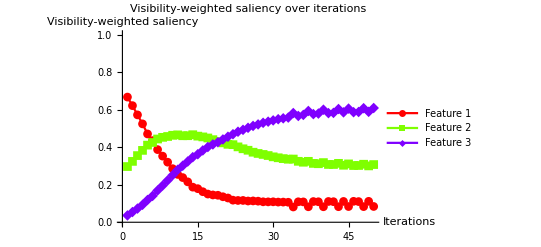

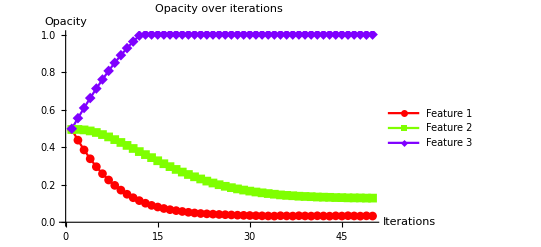

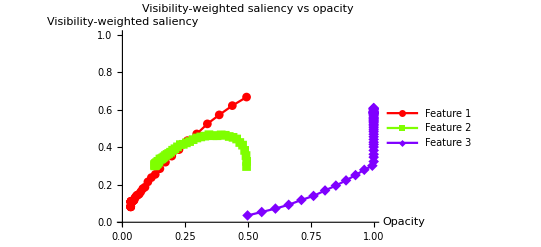

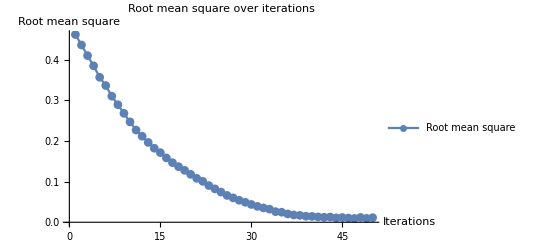

| Visibility-Weighted Saliency | Opacity | Root Mean Square | Steps
1 | 0.666905
0.29678
0.0363145 | 0.494118
0.494118
0.498039 | 0.461567 | -0.0566905
0.000321959
0.0563685
2 | 0.621306
0.324236
0.0544589 | 0.437427
0.49444
0.554408 | 0.435875 | -0.0521306
-0.00242356
0.0545541
3 | 0.572024
0.355156
0.0728192 | 0.385297
0.492016
0.608962 | 0.409784 | -0.0472024
-0.00551563
0.0527181
4 | 0.524111
0.382874
0.0930152 | 0.338094
0.4865
0.66168 | 0.384609 | -0.0424111
-0.00828737
0.0506985
5 | 0.470485
0.410824
0.118692 | 0.295683
0.478213
0.712378 | 0.356463 | -0.0370485
-0.0110824
0.0481308
6 | 0.434817
0.424918
0.140265 | 0.258635
0.467131
0.760509 | 0.336186 | -0.0334817
-0.0124918
0.0459735
7 | 0.387039
0.44355
0.169411 | 0.225153
0.454639
0.806483 | 0.310056 | -0.0287039
-0.014355
0.0430589
8 | 0.352278
0.452337
0.195385 | 0.196449
0.440284
0.849542 | 0.289001 | -0.0252278
-0.0152337
0.0404615
9 | 0.320053
0.456906
0.223041 | 0.171221
0.42505
0.890003 | 0.267794 | -0.0220053
-0.0156906
0.0376959
10 | 0.285424
0.463384
0.251192 | 0.149216
0.409359
0.927699 | 0.246809 | -0.0185424
-0.0163384
0.0348808
11 | 0.254941
0.465525
0.279534 | 0.130674
0.393021
0.96258 | 0.226645 | -0.0154941
-0.0165525
0.0320466
12 | 0.237983
0.46088
0.301137 | 0.115179
0.376469
0.994627 | 0.211534 | -0.0137983
-0.016088
0.0298863
13 | 0.215277
0.461064
0.323659 | 0.101381
0.360381
1. | 0.196295 | -0.0115277
-0.0161064
0.0276341
14 | 0.186999
0.466298
0.346702 | 0.0898535
0.344274
1. | 0.182011 | -0.00869995
-0.0166298
0.0253298
15 | 0.178882
0.458801
0.362317 | 0.0811535
0.327644
1. | 0.171205 | -0.00788823
-0.0158801
0.0237683
16 | 0.162669
0.454653
0.382677 | 0.0732653
0.311764
1. | 0.158192 | -0.00626694
-0.0154653
0.0217323
17 | 0.15024
0.448937
0.400823 | 0.0669983
0.296299
1. | 0.14649 | -0.00502397
-0.0148937
0.0199177
18 | 0.145474
0.440005
0.414521 | 0.0619744
0.281405
1. | 0.136714 | -0.00454741
-0.0140005
0.0185479
19 | 0.143788
0.429848
0.426365 | 0.057427
0.267405
1. | 0.127707 | -0.00437875
-0.0129848
0.0173635
20 | 0.135819
0.422961
0.44122 | 0.0530482
0.25442
1. | 0.117776 | -0.00358187
-0.0122961
0.015878
21 | 0.129189
0.415185
0.455626 | 0.0494663
0.242124
1. | 0.107956 | -0.00291892
-0.0115185
0.0144374
22 | 0.117616
0.413347
0.469037 | 0.0465474
0.230605
1. | 0.100514 | -0.00176163
-0.0113347
0.0130963
23 | 0.116073
0.40159
0.482337 | 0.0447858
0.219271
1. | 0.0902284 | -0.00160731
-0.010159
0.0117663
24 | 0.116151
0.391454
0.492395 | 0.0431785
0.209112
1. | 0.0820638 | -0.00161508
-0.00914538
0.0107605
25 | 0.113177
0.383568
0.503255 | 0.0415634
0.199966
1. | 0.0741996 | -0.0013177
-0.00835677
0.00967447
26 | 0.113647
0.37308
0.513273 | 0.0402457
0.19161
1. | 0.0659505 | -0.00136467
-0.00730799
0.00867266
27 | 0.112281
0.366507
0.521212 | 0.038881
0.184302
1. | 0.0599488 | -0.00122806
-0.00665074
0.0078788
28 | 0.108981
0.361192
0.529826 | 0.037653
0.177651
1. | 0.0540047 | -0.000898116
-0.00611925
0.00701736
29 | 0.108617
0.355421
0.535962 | 0.0367548
0.171532
1. | 0.049148 | -0.000861654
-0.00554211
0.00640376
30 | 0.108948
0.348517
0.542535 | 0.0358932
0.165989
1. | 0.043727 | -0.000894831
-0.00485166
0.00574649
31 | 0.107464
0.343537
0.548999 | 0.0349984
0.161138
1. | 0.0389539 | -0.000746374
-0.00435369
0.00510006
32 | 0.107375
0.338967
0.553658 | 0.034252
0.156784
1. | 0.0352153 | -0.000737516
-0.00389667
0.00463418
33 | 0.106538
0.335734
0.557728 | 0.0335145
0.152887
1. | 0.0321799 | -0.000653805
-0.00357344
0.00422724
34 | 0.081416
0.336775
0.581809 | 0.0328607
0.149314
1. | 0.0260043 | 0.0018584
-0.00367749
0.00181909
35 | 0.109042
0.324679
0.56628 | 0.0347191
0.145636
1. | 0.0246838 | -0.000904158
-0.00246789
0.00337204
36 | 0.108389
0.319753
0.571858 | 0.0338149
0.143169
1. | 0.0204333 | -0.000838934
-0.0019753
0.00281424
37 | 0.0825279
0.324574
0.592899 | 0.032976
0.141193
1. | 0.0178845 | 0.00174721
-0.00245736
0.000710145
38 | 0.11032
0.313533
0.576147 | 0.0347232
0.138736
1. | 0.0169173 | -0.00103202
-0.00135325
0.00238527
39 | 0.109213
0.311773
0.579014 | 0.0336912
0.137383
1. | 0.0148759 | -0.00092129
-0.00117728
0.00209857
40 | 0.0825772
0.317831
0.599592 | 0.0327699
0.136205
1. | 0.014395 | 0.00174228
-0.00178305
0.0000407765
41 | 0.110675
0.307892
0.581434 | 0.0345121
0.134422
1. | 0.0131774 | -0.00106747
-0.000789163
0.00185663
42 | 0.109555
0.307685
0.58276 | 0.0334447
0.133633
1. | 0.0122143 | -0.000955515
-0.000768463
0.00172398
43 | 0.0829026
0.313822
0.603275 | 0.0324892
0.132865
1. | 0.0128335 | 0.00170974
-0.00138221
-0.000327525
44 | 0.110853
0.303702
0.585446 | 0.0341989
0.131483
0.999672 | 0.0106974 | -0.00108525
-0.000370169
0.00145542
45 | 0.083736
0.310832
0.605432 | 0.0331137
0.131112
1. | 0.0117098 | 0.0016264
-0.00108323
-0.000543169
46 | 0.111486
0.302193
0.586321 | 0.0347401
0.130029
0.999457 | 0.0103899 | -0.00114856
-0.000219344
0.00136791
47 | 0.110106
0.302401
0.587492 | 0.0335915
0.12981
1. | 0.00938689 | -0.00101062
-0.000240134
0.00125076
48 | 0.083324
0.309075
0.607601 | 0.0325809
0.12957
1. | 0.0118071 | 0.0016676
-0.000907527
-0.000760078
49 | 0.111452
0.300277
0.58827 | 0.0342485
0.128662
0.99924 | 0.0094661 | -0.00114524
-0.0000277353
0.00117297
50 | 0.0840303
0.307331
0.608638 | 0.0331032
0.128634
1. | 0.0113049 | 0.00159697
-0.000733142
-0.000863829

```mathematica
t2-t1
iteration
saliency1=ListLinePlot[Transpose[#&@@@list],PlotLegends->{"Feature 1","Feature 2","Feature 3","Feature 4"},PlotLabel->"Visibility-weighted saliency over iterations",PlotRange->{All,{0,1}},PlotStyle->chartcolors,PlotMarkers->Automatic,AxesLabel->{"Iterations","Visibility-weighted saliency"}]
Export[NotebookDirectory[]<>"saliency_fixed.png",saliency1];
opacity1=ListLinePlot[Transpose[#2&@@@list],PlotLegends->{"Feature 1","Feature 2","Feature 3","Feature 4"},PlotLabel->"Opacity over iterations",PlotRange->{All,{0,1}},PlotStyle->chartcolors,PlotMarkers->Automatic,AxesLabel->{"Iterations","Opacity"}]
Export[NotebookDirectory[]<>"opacity_fixed.png",opacity1];
x=Transpose[#2&@@@list];
y=Transpose[#&@@@list];
ListLinePlot[{Transpose[{x[[1]],y[[1]]}],Transpose[{x[[2]],y[[2]]}],Transpose[{x[[3]],y[[3]]}]},PlotStyle->chartcolors,PlotLabel->"Visibility-weighted saliency vs opacity",AxesLabel->{"Opacity","Visibility-weighted saliency"},PlotLegends->{"Feature 1","Feature 2","Feature 3","Feature 4"},PlotRange->{{0,1},{0,1}},PlotMarkers->Automatic]
rms1=ListLinePlot[#3&@@@list,PlotLegends->{"Root mean square"},PlotLabel->"Root mean square over iterations",PlotRange->{All,All},PlotMarkers->Automatic,AxesLabel->{"Iterations","Root mean square"}]
Export[NotebookDirectory[]<>"rms_fixed.png",rms1];
table1=TableForm[list,TableHeadings->{Automatic,{"Visibility-Weighted Saliency","Opacity", "Root Mean Square","Steps"}},TableSpacing->{2,3}]
Export[NotebookDirectory[]<>"table_fixed.png",table1];
(*path1=Prepend[#2&@@@list,alpha[[#]]&/@index];*)
path1=#2&@@@list;
AppendTo[records,{t2-t1,iteration,Last[path1]}];
```

```mathematica
(*alpha0[[#]]&/@index0
peaks=alpha[[#]]&/@index;
MapIndexed[(alpha0[[#]]=peaks[[First@#2]])&,index0]*)
(*(*first order newton*)
target={0.1,0.3,0.6};
stepsize=0.1;
previous={{0,0,0},{0,0,0}};
list=Table[Module[{peaks,mean,steps,rms,f1,f0,diff,square,derivative,xx,dx,yy,df,factor},
mean=visibility[Interpolation[Transpose[{intensity0,alpha0}],InterpolationOrder->1]];
rms=RootMeanSquare[mean-target];
peaks=alpha0[[#]]&/@index0;
derivative=2*(mean-target);
square=(mean-target)^2;
If[Norm[First@previous]>0,{f1,f0,xx,yy}=previous,{f1,f0,xx,yy}={derivative,square,peaks,mean}];
(*diff=mean-y1;
steps=If[Product[diff[[i]],{i,Length[diff]}]≠0,(target-mean)*(peaks-x1)/(mean-y1)*stepsize,2*(target-mean)*stepsize];*)
(*dx=peaks-xx;
df=If[Product[dx[[i]],{i,Length[dx]}]≠0,(mean-yy)/dx,1];*)
(*derivative=derivative*df;*)
diff=derivative-f1;
previous={derivative,square,peaks,mean};
df=If[Product[diff[[i]],{i,Length[diff]}]≠0,-(square-f0)/diff*stepsize,-derivative*stepsize];
dx=-derivative*stepsize;
steps=Table[If[Abs[dx[[i]]]>Abs[df[[i]]],dx[[i]],df[[i]]],{i,Length[mean]}];
(*steps=If[Product[diff[[i]],{i,Length[diff]}]≠0,-derivative*(peaks-xx)/diff*stepsize,-derivative*stepsize];*)
(*steps=-derivative*stepsize;*)
peaks=Clip[peaks+steps,{0,1}];
MapIndexed[(alpha0[[#]]=peaks[[First@#2]])&,index0];
{mean,peaks,rms,steps,dx,df,Table[Abs[df[[i]]]>Abs[dx[[i]]],{i,Length[dx]}]}
],{30}];*)
```

```mathematica
(*reset peak control points*)
alpha0[[#]]&/@index0;
peaks=alpha[[#]]&/@index;
MapIndexed[(alpha0[[#]]=peaks[[First@#2]])&,index0];
(*parallel gradient*)
multipliers={1,2,4,8};
previous={0,0,0};
iteration=0;
t1=AbsoluteTime[];
t2=0;
list=Table[Module[{peaks,mean,steps,rms,meanlist,peaklist,rmslist,minindex},
mean=If[Norm[previous]>0,previous,Visibility[Interpolation[Transpose[{intensity0,alpha0}],InterpolationOrder->1]]];
rms=RootMeanSquare[mean-target];
peaks=alpha0[[#]]&/@index0;
steps=-2*(mean-target)*stepsize;
peaklist=ParallelMap[Clip[peaks+steps*#,{0,1}]&,multipliers];
meanlist=ParallelMap[VisibilitySaliency[#]&,peaklist];
rmslist=ParallelMap[RootMeanSquare[#-target]&,meanlist];
minindex=First@Ordering[rmslist,1];
MapIndexed[(alpha0[[#]]=peaklist[[minindex]][[First@#2]])&,index0];
previous=meanlist[[minindex]];
If[t2==0 && rmslist[[minindex]]<epsilon,t2=AbsoluteTime[];iteration=iterator];
{mean,peaks,rms,steps,multipliers[[minindex]]}
],{iterator,10}];
```

33.772996

6

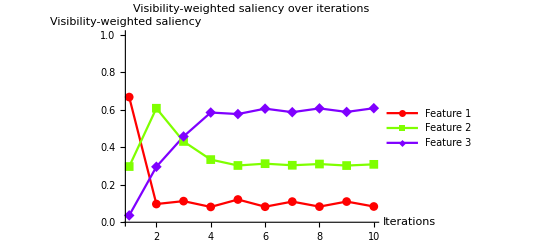

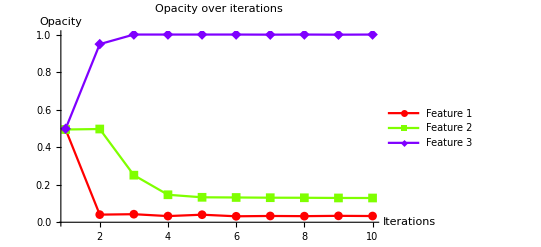

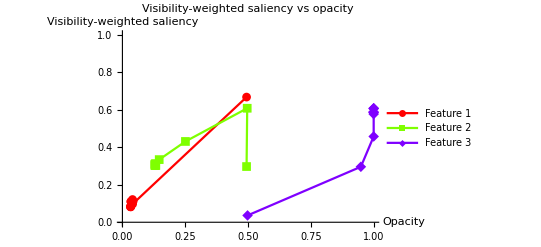

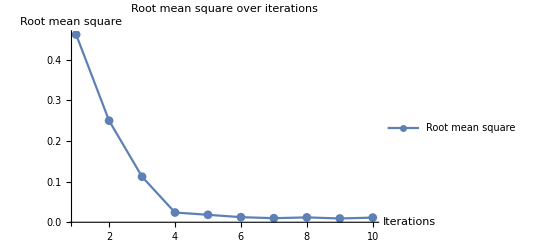

| Visibility-Weighted Saliency | Opacity | Root Mean Square | Steps | Multiplier
1 | 0.666905
0.29678
0.0363145 | 0.494118
0.494118
0.498039 | 0.461567 | -0.0566905
0.000321959
0.0563685 | 8
2 | 0.0971045
0.607334
0.295561 | 0.0405936
0.496693
0.948988 | 0.249764 | 0.000289548
-0.0307334
0.0304439 | 8
3 | 0.112551
0.430454
0.456995 | 0.04291
0.250826
1. | 0.111992 | -0.00125509
-0.0130454
0.0143005 | 8
4 | 0.0816349
0.333807
0.584559 | 0.0328692
0.146462
1. | 0.0239347 | 0.00183651
-0.00338066
0.00154415 | 4
5 | 0.12116
0.302399
0.576441 | 0.0402153
0.13294
1. | 0.0183352 | -0.00211602
-0.000239902
0.00235592 | 4
6 | 0.0827665
0.312072
0.605161 | 0.0317512
0.13198
1. | 0.0125083 | 0.00172335
-0.00120724
-0.000516105 | 1
7 | 0.109987
0.303605
0.586407 | 0.0334746
0.130773
0.999484 | 0.00995855 | -0.000998749
-0.000360548
0.0013593 | 1
8 | 0.0832406
0.310167
0.606592 | 0.0324758
0.130412
1. | 0.0119402 | 0.00167594
-0.00101669
-0.000659243 | 1
9 | 0.110241
0.302042
0.587718 | 0.0341518
0.129396
0.999341 | 0.00930764 | -0.00102407
-0.000204169
0.00122824 | 1
10 | 0.0839149
0.30848
0.607605 | 0.0331277
0.129191
1. | 0.0113795 | 0.00160851
-0.000848037
-0.000760471 | 1

```mathematica
t2-t1
iteration
saliency2=ListLinePlot[Transpose[#&@@@list],PlotLegends->{"Feature 1","Feature 2","Feature 3","Feature 4"},PlotLabel->"Visibility-weighted saliency over iterations",PlotRange->{All,{0,1}},PlotStyle->chartcolors,PlotMarkers->Automatic,AxesLabel->{"Iterations","Visibility-weighted saliency"}]
Export[NotebookDirectory[]<>"saliency_parallelsearch.png",saliency2];
opacity2=ListLinePlot[Transpose[#2&@@@list],PlotLegends->{"Feature 1","Feature 2","Feature 3","Feature 4"},PlotLabel->"Opacity over iterations",PlotRange->{All,{0,1}},PlotStyle->chartcolors,PlotMarkers->Automatic,AxesLabel->{"Iterations","Opacity"}]
Export[NotebookDirectory[]<>"opacity_parallelsearch.png",opacity2];
x=Transpose[#2&@@@list];
y=Transpose[#&@@@list];
ListLinePlot[{Transpose[{x[[1]],y[[1]]}],Transpose[{x[[2]],y[[2]]}],Transpose[{x[[3]],y[[3]]}]},PlotStyle->chartcolors,PlotLabel->"Visibility-weighted saliency vs opacity",AxesLabel->{"Opacity","Visibility-weighted saliency"},PlotLegends->{"Feature 1","Feature 2","Feature 3","Feature 4"},PlotRange->{{0,1},{0,1}},PlotMarkers->Automatic]
rms2=ListLinePlot[#3&@@@list,PlotLegends->{"Root mean square"},PlotLabel->"Root mean square over iterations",PlotRange->{All,All},PlotMarkers->Automatic,AxesLabel->{"Iterations","Root mean square"}]
Export[NotebookDirectory[]<>"rms_parallelsearch.png",rms2];
table2=TableForm[list,TableHeadings->{Automatic,{"Visibility-Weighted Saliency","Opacity", "Root Mean Square","Steps","Multiplier"}},TableSpacing->{2,3}]
Export[NotebookDirectory[]<>"table_parallelsearch.png",table2];
(*path2=Prepend[#2&@@@list,alpha[[#]]&/@index];*)
path2=#2&@@@list;
AppendTo[records,{t2-t1,iteration,Last[path2]}];
```

```mathematica
(*reset peak control points*)
alpha0[[#]]&/@index0;
peaks=alpha[[#]]&/@index;
MapIndexed[(alpha0[[#]]=peaks[[First@#2]])&,index0];
(*line search*)
previous={0,0,0};
iteration=0;
t1=AbsoluteTime[];
t2=0;
list=Table[Module[{peaks,mean,steps,rms,peaklist,minindex,minrms,minmean,rms2,mean2},
mean=If[Norm[previous]>0,previous,Visibility[Interpolation[Transpose[{intensity0,alpha0}],InterpolationOrder->1]]];
rms=RootMeanSquare[mean-target];
peaks=alpha0[[#]]&/@index0;
steps=-2*(mean-target)*stepsize;
peaklist=Map[Clip[peaks+steps*#,{0,1}]&,multipliers];
minindex=1;
minmean=VisibilitySaliency[peaklist[[minindex]]];
minrms=RootMeanSquare[minmean-target];
Do[mean2=VisibilitySaliency[peaklist[[i]]];
rms2=RootMeanSquare[mean2-target];
If[rms2<minrms,minrms=rms2;minmean=mean2;minindex=i,Return[i]];
,{i,Range[2,4]}];
MapIndexed[(alpha0[[#]]=peaklist[[minindex]][[First@#2]])&,index0];
previous=minmean;
If[t2==0 && minrms<epsilon,t2=AbsoluteTime[];iteration=iterator];
{mean,peaks,rms,steps,multipliers[[minindex]]}
],{iterator,10}];
```

```mathematica
t2-t1
iteration
saliency3=ListLinePlot[Transpose[#&@@@list],PlotLegends->{"Feature 1","Feature 2","Feature 3","Feature 4"},PlotLabel->"Visibility-weighted saliency over iterations",PlotRange->{All,{0,1}},PlotStyle->chartcolors,PlotMarkers->Automatic,AxesLabel->{"Iterations","Visibility-weighted saliency"}]
Export[NotebookDirectory[]<>"saliency_linesearch.png",saliency3];
opacity3=ListLinePlot[Transpose[#2&@@@list],PlotLegends->{"Feature 1","Feature 2","Feature 3","Feature 4"},PlotLabel->"Opacity over iterations",PlotRange->{All,{0,1}},PlotStyle->chartcolors,PlotMarkers->Automatic,AxesLabel->{"Iterations","Opacity"}]
Export[NotebookDirectory[]<>"opacity_linesearch.png",opacity3];
x=Transpose[#2&@@@list];
y=Transpose[#&@@@list];
ListLinePlot[{Transpose[{x[[1]],y[[1]]}],Transpose[{x[[2]],y[[2]]}],Transpose[{x[[3]],y[[3]]}]},PlotStyle->chartcolors,PlotLabel->"Visibility-weighted saliency vs opacity",AxesLabel->{"Opacity","Visibility-weighted saliency"},PlotLegends->{"Feature 1","Feature 2","Feature 3","Feature 4"},PlotRange->{{0,1},{0,1}},PlotMarkers->Automatic]
rms3=ListLinePlot[#3&@@@list,PlotLegends->{"Root mean square"},PlotLabel->"Root mean square over iterations",PlotRange->{All,All},PlotMarkers->Automatic,AxesLabel->{"Iterations","Root mean square"}]
Export[NotebookDirectory[]<>"rms_linesearch.png",rms3];
table3=TableForm[list,TableHeadings->{Automatic,{"Visibility-Weighted Saliency","Opacity", "Root Mean Square","Steps","Multiplier"}},TableSpacing->{2,3}]
Export[NotebookDirectory[]<>"table_linesearch.png",table3];
(*path3=Prepend[#2&@@@list,alpha[[#]]&/@index];*)
path3=#2&@@@list;
AppendTo[records,{t2-t1,iteration,Last[path3]}];
```

60.1708628

6

-Graphics-

-Graphics-

-Graphics-

-Graphics-

| Visibility-Weighted Saliency | Opacity | Root Mean Square | Steps | Multiplier
1 | 0.666905
0.29678
0.0363145 | 0.494118
0.494118
0.498039 | 0.461567 | -0.0566905
0.000321959
0.0563685 | 8
2 | 0.0971045
0.607334
0.295561 | 0.0405936
0.496693
0.948988 | 0.249764 | 0.000289548
-0.0307334
0.0304439 | 8
3 | 0.112551
0.430454
0.456995 | 0.04291
0.250826
1. | 0.111992 | -0.00125509
-0.0130454
0.0143005 | 8
4 | 0.0816349
0.333807
0.584559 | 0.0328692
0.146462
1. | 0.0239347 | 0.00183651
-0.00338066
0.00154415 | 4
5 | 0.12116
0.302399
0.576441 | 0.0402153
0.13294
1. | 0.0183352 | -0.00211602
-0.000239902
0.00235592 | 4
6 | 0.0827665
0.312072
0.605161 | 0.0317512
0.13198
1. | 0.0125083 | 0.00172335
-0.00120724
-0.000516105 | 1
7 | 0.109987
0.303605
0.586407 | 0.0334746
0.130773
0.999484 | 0.00995855 | -0.000998749
-0.000360548
0.0013593 | 1
8 | 0.0832406
0.310167
0.606592 | 0.0324758
0.130412
1. | 0.0119402 | 0.00167594
-0.00101669
-0.000659243 | 1
9 | 0.110241
0.302042
0.587718 | 0.0341518
0.129396
0.999341 | 0.00930764 | -0.00102407
-0.000204169
0.00122824 | 1
10 | 0.0839149
0.30848
0.607605 | 0.0331277
0.129191
1. | 0.0113795 | 0.00160851
-0.000848037
-0.000760471 | 1

```mathematica
recordxml=NotebookDirectory[]<>"~images\\records.xml";
recordmap=If[FileExistsQ[recordxml],Association@Import[recordxml],<||>];
AssociateTo[recordmap,dataname->records];
Export[recordxml,Normal[recordmap]];
dataname->records
```

CT-Knee_naive→{{121.516945,47,{0.0331032,0.128634,1.}},{33.772996,6,{0.0331277,0.129191,1.}},{60.1708628,6,{0.0331277,0.129191,1.}}}

```mathematica
(*range=Range[0,1,0.1];
coordinates=Flatten[Table[{i,j,k},{i,range},{j,range},{k,range}],2];
Length[coordinates]
Clear[f];
Clear[data];
AbsoluteTiming[
searchspace=ParallelTable[Module[{mean,rms},
mean=VisibilitySaliency[c];
rms=RootMeanSquare[mean-target];
{mean,c,rms}
],{c,coordinates}];
]*)
```

```mathematica
(*transform=RotationTransform[-90 Degree,{0,0,1}];
vec=transform[{1.3, -2.4, 2.}];
opacitylist=#2&@@@searchspace;
rmslist=#3&@@@searchspace;
merged=ParallelTable[Append[opacitylist[[i]],rmslist[[i]]],{i,Length[opacitylist]}];
densityplot=ListDensityPlot3D[merged,ColorFunction->"LightTemperatureMap",PlotLegends->Automatic,PlotLabel->{"x","y","z"},PlotTheme->"Detailed",OpacityFunction->Automatic];
paths={path1,path3};
pathcolors={Red,Green,Blue};
plotlegends={{"Fixed step size"},{"Adaptive step size with line search"},{"Adaptive step size with parallel search"}};
pointplots=ParallelTable[ListPointPlot3D[paths[[i]],PlotStyle->{pathcolors[[i]],Thick,PointSize[Large]},PlotLegends->plotlegends[[i]]],{i,Length[paths]}];
lineplots=ParallelTable[ListPointPlot3D[paths[[i]],PlotStyle->{pathcolors[[i]]}]/.Point->Line,{i,Length[paths]}];
sp=Show[densityplot,PlotLabel->"Objective function in parameter space",ViewPoint->vec]
sp2=Show[densityplot,pointplots[[1]],pointplots[[2]],lineplots[[1]],lineplots[[2]],PlotLabel->"Gradient descent in parameter space",ViewPoint->vec]
Export[NotebookDirectory[]<>"parameterspace.png",sp];
Export[NotebookDirectory[]<>"parameterspace_path.png",sp2];

{c1,c2,c3}=chartcolors;
blend1=Blend[{{0,Black},{0.5,c1},{1,White}},#]&;
blend2=Blend[{{0,Black},{0.5,c2},{1,White}},#]&;
blend3=Blend[{{0,Black},{0.5,c3},{1,White}},#]&;
saliencylist=#&@@@searchspace;
first=#&@@@saliencylist;
second=#2&@@@saliencylist;
third=#3&@@@saliencylist;
merged1=ParallelTable[Append[opacitylist[[i]],first[[i]]],{i,Length[opacitylist]}];
merged2=ParallelTable[Append[opacitylist[[i]],second[[i]]],{i,Length[opacitylist]}];
merged3=ParallelTable[Append[opacitylist[[i]],third[[i]]],{i,Length[opacitylist]}];
dplots=ListDensityPlot3D[#1,ColorFunction->#2,PlotLegends->Automatic,PlotTheme->"Detailed",OpacityFunction->(#&)]&@@@{{merged1,blend1},{merged2,blend2},{merged3,blend3}};
densityplots=MapIndexed[Show[#,PlotLabel->"Visibility-weighted saliency of feature "<>ToString[First@#2],ViewPoint->vec]&,dplots]
MapIndexed[Export[NotebookDirectory[]<>"densityplot"<>ToString[First@#2]<>".png",#]&,densityplots];*)
```

```mathematica
saveTransferFunction[peaks_,filename_]:=Module[{a2,rgba2,intensity2,rgbafunction2,rgba2denormalized,xrgba,strlist,alphaMode,gammaValue,domain,threshold,k,int,split,colorL,keylist,keys,TransFuncIntensity,VoreenData,xml},
MapIndexed[(alpha0[[#]]=peaks[[First@#2]])&,index0];
a2=IntegerPart[255*alpha0[[#]]]&/@rangeOfAlpha;
rgba2=(#/255.&)/@Transpose[{r,g,b,a2}]//(RGBColor/@#&);
intensity2=intensity0[[#]]&/@rangeOfAlpha;
rgbafunction2=(Blend[Transpose[{intensity2,rgba2}], #] & );(* for return only. not used in this function *)

rgba2denormalized=Transpose[{r,g,b,a2}];
xrgba=Table[Join[{intensity2[[i]]},rgba2denormalized[[i]]],{i,Length[intensity2]}];
strlist={ToString[#1],ToString[#2],ToString[#3],ToString[#4],ToString[#5]}&@@@xrgba;
alphaMode=XMLElement["alphaMode",{"value"->"1"},{}];
gammaValue=XMLElement["gammaValue",{"value"->"1"},{}];
domain=XMLElement["domain",{"x"->"0","y"->"1"},{}];
threshold=XMLElement["threshold",{"x"->"0","y"->"1"},{}];
k=({int=XMLElement["intensity",{"value"->#1},{}],split=XMLElement["split",{"value"->"false"},{}],colorL=XMLElement["colorL",{"r"->#2,"g"->#3,"b"->#4,"a"->#5},{}]}&)@@@strlist;
keylist=XMLElement["key",{"type"->"TransFuncMappingKey"},{#1,#2,#3}]&@@@k;
keys=XMLElement["Keys",{},keylist];
TransFuncIntensity=XMLElement["TransFuncIntensity",{"type"->"TransFuncIntensity"},{alphaMode,gammaValue,domain,threshold,keys}];
VoreenData=XMLElement["VoreenData",{"version"->"1"},{TransFuncIntensity}];
xml=XMLObject["Document"][{XMLObject["Declaration"]["Version"->"1.0"],XMLObject["Comment"]["This is a Voreen transfer function exported from Mathematica"]},VoreenData,{}];
Export[filename,xml, "XML"];
rgbafunction2
];
```

```mathematica
tf1=saveTransferFunction[Last[path1],NotebookDirectory[]<>"optimized_fixed.tfi"];
tf2=saveTransferFunction[Last[path2],NotebookDirectory[]<>"optimized_parallelsearch.tfi"];
tf3=saveTransferFunction[Last[path3],NotebookDirectory[]<>"optimized_linesearch.tfi"];
Image3D[d,ColorFunction->rgbafunction,ViewPoint->viewpoints[face]]
Image3D[d,ColorFunction->tf3,ViewPoint->viewpoints[face]]
ListLinePlot[Transpose[{intensity,alpha}],PlotRange->{{0,1},{0,1}},ColorFunction->rgbfunction,PlotLegends->"Before optimization"]
(*Transpose[{intensity,r,g,b,a}]*)
ListLinePlot[Transpose[{intensity0[[#]]&/@rangeOfAlpha,alpha0[[#]]&/@rangeOfAlpha}],PlotRange->{{0,1},{0,1}},ColorFunction->rgbfunction,PlotLegends->"After optimization"]
(*xrgba*)
```

-Graphics-

-Graphics-